90 points. An A- paper

# M154 Spring 2013 Lesson 2

## Mario L Gutierrez

```mathematica
Clear["Global`*"]
```

## Elementary Calculus:

```mathematica
Clear["Global`*"]
```

Read S 8.1 and 8.2, 9.1,9.2.

Not surprisingly Mathematica can compute limits,derivatives and integrals

### Limits

Query Limit. As usual  read the Details and Options section in the documentation. Be sure you understand the Direction option

Illustrating S p 202  example 2 graphically:

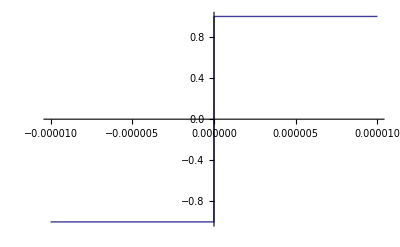

```mathematica
Plot[x/Abs[x],{x,-1/100000,1/100000}]
```

A function with two horizontal asymptotes:

```mathematica
Limit[x/(√(1+x^2)),x->-∞]
```

-1

```mathematica
Limit[x/(√(1+x^2)),x->∞]
```

1

Illustrating graphically (see S 2.9 example 2 for ploting several expressions

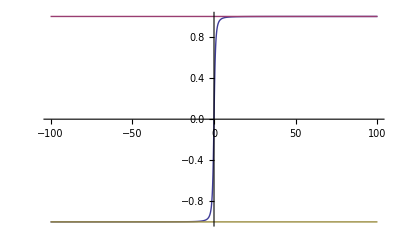

```mathematica
Plot[{x/(√(1+x^2)),1,-1},{x,-100,100}]
```

Problem 1 (10 points) a: Use Mathematica to compute

limit_(x→0^-) ⅇ^(1/x) and limit_(x→0^+) ⅇ^(1/x)

(Remember that in Mathematica e is just a symbol, the base of the natural logarithms ⅇ, is typed from the basic math input palette or by the keyboard shortcut EsceeEsc)

```mathematica
Limit[Exp[1/x],x->0,Direction->1]
```

0

```mathematica
Limit[Exp[1/x],x->0,Direction->-1]
```

∞

b: Illustrate your results with a plots over [-1,0) and over (0,1]

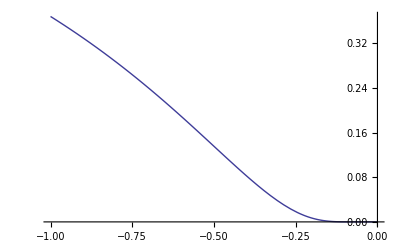

```mathematica
Plot[Exp[1/x],{x,-1,0}]
```

As we can easily notice from the graph above, as the variable x approaches 0 from the left  the function ⅇ^(1/x) approaches 0 as well.

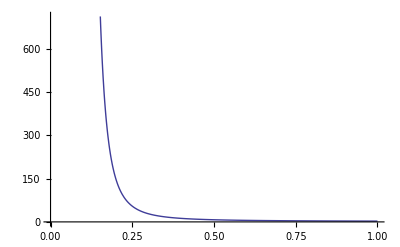

```mathematica
Plot[Exp[1/x],{x,0,1}]
```

In this case as x approaches 0 from the right the function ⅇ^(1/x) goes to infinity.

10 points

#### Some limitations of Mathematica

Mathematica is capable of working with very large and very small numbers but the are bounds (which are determined by the machine on which you are working ) on the size of the numbers with which Mathematica can work . These bounds are determined by the Mathematica variables $MaxNumber and $MinNumber.

Read $MaxNumber and $MinNumber.

Execute the commands $MaxNumber and $MinNumber on your computer. When I bought my computer a couple of years ago I got lots of memory and my results are:

```mathematica
$MaxNumber
```

8.7681267068286973894018490599070588851`15.954589770191005*^2711437152599256

```mathematica
$MinNumber
```

1.14049446755963386306579044221896413086`15.954589770191005*^-2711437152599257

The results depend on how much memory you have

At least on my computer if I try to work with an integer with more than 2711437152599256 digits or an number with absolute value larger than 8.7681267068286973894018490599070588851`15.954589770191005*^2711437152599256 digits Mathematica will give a message concerning Overflow  This is Mathematica saying that magnitude of the number is very large but the magnitude is too big to  work with on my computer. If you try to work with a number whose magnitude is smaller than 1.14049446755963386306579044221896413086`15.954589770191005*^-2711437152599257 Mathematica will output a message about Underflow. This is Mathematica telling you that the magnitude is very small but too small to work with on your computer

```mathematica
?Overflow
```

RowBox[{"Overflow", "[", "]"}] represents a number too large to represent explicitly on your computer system.

```mathematica
?Underflow
```

Underflow[] represents a number too small to represent explicitly on your computer system.

#### Symbolic vs. Numerical Computation

It is important to consider the difference between exact and inexact computation. Given a function f there is a  difference between the computation of N[f[x],k] and f[N[x,k]], for x an exact number. In the first case we are asking Mathematica to perform (a possibly extensive) exact computation and then give us an inexact approximation of the result of this computation. Whereas N[x,k] gives an inexact number and then Mathematica can evaluate f[N[x,k]] using less computationally intensive inexact methods and with lower risk of underflows and overflows.

### D

Read S 205-207. Also read Differentiation and R 19.1. It is important to note that unless a variable, e.g. y, is explicitly given as a function of the variable with respect to which we are differentiating, e.g.. z, Mathematica assumes that y is a constant.

```mathematica
D[y,z]
```

0

```mathematica
D[y^2 z^2,z]
```

2 y^2 z

```mathematica
D[y[z]^2 z,z]
```

y[z]^2+2 z y[z] y'[z]

```mathematica
f'[z]/g[z]-(f[z] g'[z])/g[z]^2//Together
```

```mathematica
D[f[g[z]],z]
```

f'[g[z]] g'[z]

Higher derivatives:

```mathematica
D[x^4,{x,3}]
```

24 x

```mathematica
D[f[g[z]],{z,2}]
```

g'[z]^2 f''[g[z]]+f'[g[z]] g''[z]

Partial derivatives: 
Example (∂^2 x^n y^m)/(∂x∂y)

```mathematica
D[x^n y^m,x,y]
```

m n x^(-1+n) y^(-1+m)

Example (∂^5 x^n y^m)/(∂^2 x∂^3 y)

```mathematica
D[x^n y^m,{x,2},{y,3}]
```

(-2+m) (-1+m) m (-1+n) n x^(-2+n) y^(-3+m)

D has an option NonConstants which tells Mathematica that when differentiating with respect to variable v other symbols should be treated implicitly as variables of z

```mathematica
D[a z+a^2+a b,z]
```

a

```mathematica
D[a z+a^2+a b,z,NonConstants->{a}]
```

a+2 a D[a,z,NonConstants→{a}]+b D[a,z,NonConstants→{a}]+z D[a,z,NonConstants→{a}]

```mathematica
D[a b,z,NonConstants->{a,b}]
```

b D[a,z,NonConstants→{a,b}]+a D[b,z,NonConstants→{a,b}]

With this option we can do implicit differentiation.

```mathematica
eq =x^2 y+ⅇ^y==Sin[y]
```

ⅇ^y+x^2 y==Sin[y]

```mathematica
D[eq,x,NonConstants->{y}]
```

2 x y+ⅇ^y D[y,x,NonConstants→{y}]+x^2 D[y,x,NonConstants→{y}]==Cos[y] D[y,x,NonConstants→{y}]

### Integrate

D is a straightforward command and at least in theory for any computation of D[expr,{z,n}] we should with enough time be able to do the differentiation by hand.

Read S 226-229. Query Integrate and NIntegrate. Observe that Mathematica’s evaluation of roots of negative numbers carries over to definite integrals:

```mathematica
∫x^(1/3)ⅆx
```

(3 x^(4/3))/4

```mathematica
Integrate[x^(1/3),{x,-1,0}]
```

3/4 (-1)^(1/3)

```mathematica
NIntegrate[x^(1/3),{x,-1,0}]
```

0.375+0.649519 ⅈ

Inside the cover of most calculus texts are incomplete tables of integrals. Once upon a time people used much more comprehensive table of integrals in order to find indefinite integrals.

Unlike D, Integrate is a much more sophisticated command in that it can compute integrals that are not found in such tables. (It is amusing to note that symbolic manipulation programs grew out of the computer science problem of doing indefinite integrals.)

```mathematica
∫√(1+x^4)ⅆx
```

(x+x^5-2 (-1)^(1/4) √(1+x^4) EllipticF[ⅈ ArcSinh[(-1)^(1/4) x],-1])/(3 √(1+x^4))

Notice that our answers are often given in terms of sophisticated transcendental functions that you probably haven’t seen before, and also in terms of complex numbers. Even definite integrals that ought to be real can end up as expressions that contain complex numbers (in the end the imaginary parts ought to cancel but performing Mathematica manipulations that do these cancellations may be impossible

```mathematica
∫_1^2 1/√(1+x^2+x^4)ⅆx
```

-(-1)^(2/3) EllipticF[ArcSin[1+ⅈ √3],1/2 ⅈ (ⅈ+√3)]-ⅈ √(1+(-1)^(2/3)) EllipticF[ⅈ ArcSinh[(-1)^(5/6)],(-1)^(2/3)]

```mathematica
ComplexExpand[-(-1)^(2/3) EllipticF[ArcSin[1+ⅈ √3],1/2 ⅈ (ⅈ+√3)]-ⅈ √(1+(-1)^(2/3)) EllipticF[ⅈ ArcSinh[(-1)^(5/6)],(-1)^(2/3)]]
```

1/2 √3 Im[EllipticF[ArcSin[1+ⅈ √3],1/2 ⅈ (ⅈ+√3)]]+1/2 √3 Im[EllipticF[ⅈ ArcSinh[(-1)^(5/6)],(-1)^(2/3)]]+1/2 Re[EllipticF[ArcSin[1+ⅈ √3],1/2 ⅈ (ⅈ+√3)]]+1/2 Re[EllipticF[ⅈ ArcSinh[(-1)^(5/6)],(-1)^(2/3)]]+ⅈ (1/2 Im[EllipticF[ArcSin[1+ⅈ √3],1/2 ⅈ (ⅈ+√3)]]+1/2 Im[EllipticF[ⅈ ArcSinh[(-1)^(5/6)],(-1)^(2/3)]]-1/2 √3 Re[EllipticF[ArcSin[1+ⅈ √3],1/2 ⅈ (ⅈ+√3)]]-1/2 √3 Re[EllipticF[ⅈ ArcSinh[(-1)^(5/6)],(-1)^(2/3)]])

Also there are some integrals that Mathematica just can’t do

```mathematica
∫_4^7 Sin[Cos[x]]ⅆx
```

∫_4^7 Sin[Cos[x]]ⅆx

However if we just want to know the numerical value of integrals we use NIntegrate, which is just a much more sophisticated version of Riemann sums.

```mathematica
NIntegrate[Sin[Cos[x]],{x,4,7}]
```

1.22623

```mathematica
NIntegrate[Sin[Cos[x]],{x,4,7},WorkingPrecision->50]
```

1.2262340111833951080409497399152754420223406853053

## User defined functions

Read S.2.10. When defining a function f[var_]:=expr or f[var_]=expr  it is essential to include the underscore _ otherwise Mathematica will only know how to evaluate f[var]. Thus:

```mathematica
f[z_]=z^2
```

z^2

```mathematica
f[z]
```

z^2

```mathematica
f[2]
```

4

```mathematica
g[z]=z^2
```

z^2

```mathematica
g[z]
```

z^2

```mathematica
g[2]
```

g[2]

```mathematica
Clear[f,g]
```

### Difference between f[var_]:=expr and f[var_]=expr

Read R 17.1.1

Much like immediate x=y and delayed assignment x:=y, there are two syntaxes for the definition of user defined functions f[var_]=expr and f[var_]:=expr. In either case expr is called the body of the function. The difference of the two syntaxes is as follows : In the case of the input f[var_]=expr, Mathematica evaluates expr to get expr1, which is output and then when f[z] is input z is substituted into expr1 getting expr2 and then expr2 is evaluated and output. In the case of f[var_]:=expr there is not output. When f[z] is input, z is substituted into expr  getting expr3 and then expr3 is evaluated and output. Most of the time we want the second case so we use the f[var_]:=expr syntax. It is important to notice that with this syntax we get no output, and so in order to be sure we have input the desired expr it is a good idea to evalaute the function on a variable and specific values where we know what the output should be. Also If we have defined a function and then later on we wish to recall the definition of the function we can use the ? syntax. Example: Suppose we want to define a function which is suppose to evaluate to Sin+Cos

```mathematica
ex[x_]:=Sin[x]+Cos[x]
```

No output.

Evaluating on a variable:

```mathematica
ex[z]
```

Cos[z]+Sin[z]

Evaluating on a specific value:

```mathematica
ex[π/4]
```

√2

Using the ? syntax

```mathematica
?ex
```

Global`ex

ex[x_]:=Sin[x]+Cos[x]

```mathematica
Clear[ex]
```

Be sure you understand the point of the examples in R p513-512. We give another example: Consider the difference between

```mathematica
delayed[u_]:=D[ⅇ^(u^2)u,u]
```

```mathematica
immediate[u_]=D[ⅇ^(u^2)u,u]
```

ⅇ^(u^2)+2 ⅇ^(u^2) u^2

```mathematica
immediate[2]
```

9 ⅇ^4

Mathematica  computes D[ⅇ^(u^2)u ,u] gets ⅇ^(u^2)+2 ⅇ^(u^2) u^2  sustitutes 2 into ⅇ^(u^2)+2 ⅇ^(u^2) u^2 and gets 9 ⅇ^4

but

```mathematica
delayed[2]
```

General::ivar: 2 is not a valid variable.

∂_2 (2 ⅇ^4)

when computing delayed[2] Mathematica substitutes 2 into D[ⅇ^(u^2)u ,u]   gets  D[ⅇ^(2^2)2,2] and then evaluates giving a warning message that 2 is not a variable.

```mathematica
Clear[immediate,delayed]
```

### Anonymous or Pure Functions

Read S A.1 p332 and  pure functions . We will also call pure functions  anonymous functions, in the sense that we work with these functions without explicitly defining them or naming them.

Naming a function:

```mathematica
example[z_]:=3 z^5+Cos[z]+ⅇ^Sin[z]
```

```mathematica
example[a]
```

3 a^5+ⅇ^Sin[a]+Cos[a]

Using the Function[var,body] syntax:

```mathematica
Function[var,3 var^5+Cos[var]+ⅇ^Sin[var]][a]
```

3 a^5+ⅇ^Sin[a]+Cos[a]

Using the # & syntax

```mathematica
3#^5+Cos[#]+ⅇ^Sin[#]&[a]
```

3 a^5+ⅇ^Sin[a]+Cos[a]

The second syntax is the one we will use most often.

```mathematica
Clear[example]
```

In contradiction to S A.1 it is not the case that we can do Mathematica without knowing the concept of anonymous function so we quote from a book which I recommend very highly.Mathematica: A Problem Centered Approach by Roozbeh Hazrat. :

“Sometimes we need to “define a function as we go” and use it on the spot. Mathematica enables us to define a function without giving it a name , use it, and then go on. These functions are called anonymous or pure functions. Obviously if we want to use a specific function frequently then the best way is to give it a name”

S p 312 gives an example where the output to a Mathematica command is given in terms of a pure function.

Query Root. We will discuss solving equations in the next lesson but often solutions to equations are given in terms of Root evaluated on anonymous functions.

### Operators

Read S 2.11

Let S be a set of functions. A function f :S→R is called an operator. The most well known operator is the differentiation operator. S is the set of differentiable functions, R is the set of functions and 
d/dx:f→f'. More generally we have n-th derivative operator d^n/(d x^n):f→f^(n). In Mathematica these operators are given by Derivative[1][f], Derivative[n][f]

```mathematica
Derivative[1][Sin]
```

Cos[#1]&

```mathematica
Derivative[3][Cos]
```

Sin[#1]&

```mathematica
Derivative[1][#^3+ⅇ^(#^2)&]
```

2 ⅇ^(#1^2) #1+3 #1^2&

```mathematica
g[x_]:=Sin[x]+√x
```

```mathematica
Derivative[1][g]
```

```mathematica
Cos[#1]+1/(2 √#1)&
Derivative[2][g]
```

Cos[#1]+1/(2 √#1)&

-Sin[#1]-1/(4 #1^(3/2))&

Notice that the output of the derivative operator is given in terms of pure functions.

```mathematica
Clear[g]
```

```mathematica
Derivative[1][Sin][x]
```

Cos[x]

Given a function f we can also denote the derivative function by f'.

```mathematica
FullForm[f']
```

Derivative[1][f]

```mathematica
FullForm[g'']
```

Derivative[2][g]

An operator is called functional if its values are also functions. In order to understand a functional operator O we need to know O[f][x]. Mathematica has a number of built-in operators. We have just seen Derivative. S p 57 discusses Composition. Query InverseFunction.

```mathematica
InverseFunction[Exp]
```

Log

```mathematica
InverseFunction[Sin]
```

ArcSin

```mathematica
Derivative[1][InverseFunction[f]]
```

1/f'[f^(-1)[#1]]&

```mathematica
Derivative[1][InverseFunction[f]][x]
```

1/f'[f^(-1)[x]]

```mathematica
D[InverseFunction[f][x],x]
```

1/f'[f^(-1)[x]]

```mathematica
D[InverseFunction[f][x],{x,2}]
```

-f''[f^(-1)[x]]/(f'[f^(-1)[x]]^3)

```mathematica
Derivative[3][InverseFunction[f]][x]
```

(3 f''[f^(-1)[x]]^2)/(f'[f^(-1)[x]]^5)-(f^(3)[f^(-1)[x]])/(f'[f^(-1)[x]]^4)

S example 68 gives a way of defining  algebraic combinations of functions.  The next problem asks you to define operators, sum, product, and quotient.  Furthermore I want you to use pure functions.

First let us build the operator Composition by hand

```mathematica
composition[f_,g_]:=f[g[#]]&
```

```mathematica
composition[h,k][x]
```

h[k[x]]

Observe as usual we use lowercase letters to begin variables and user constructed functions in order to avoid clashing with built  in Mathematica expressions.

Problem 2  (15 points)
a:Define operator the operator sum so that for functions f,g we have sum[f,g][x]=f[x]+g[x]. As in the construction of the operator composition use pure functions. Check that your results are correct by evaluating sum[h,k][x] and sum[Sin,Cos][π/4].

```mathematica
sum[f_,g_]:=f[#]+g[#]&
```

```mathematica
sum[h,k][x]
```

h[x]+k[x]

```mathematica
sum[Sin,Cos][π/4]
```

√2

b: Similarly define the operator product with product[h,k][x]=h[x]k[x]. Use pure functions and check your results.

```mathematica
product[f_,g_]:=f[#]*g[#]&
```

```mathematica
product[h,k][x]
```

h[x] k[x]

```mathematica
product[Sin,Cos][π/4]
```

1/2

c: As in a: and b: define the operator quotient such that quotient[f,g][x]=f[x]/g[x]. Use pure functions and check your results

```mathematica
quotient[f_,g_]:=f[#]/g[#]&
```

```mathematica
quotient[h,k][x]
```

h[x]/k[x]

```mathematica
quotient[Sin,Cos][π/4]
```

1

15 points

#### Operator newt

Look up Newton's method in you calculus text. Try to read

```mathematica
Hyperlink["Newton-Raphson Method","http://en.wikipedia.org/wiki/Newton's_method"]
```

(By the way if you want to put a link in a notebook the syntax is Hyperlink[“label”,”URL”]

Problem3:(10 points) Define the operator newt such that newt (f) (x) =x-(f(x))/(f'(x)). Make the values of newt pure functions

```mathematica
newt[f_]:=#-f[#]/(Derivative[1][f[#]])&
```

```mathematica
newt[f][x]
```

x-f[x]/(f[x]')

10 points

We will be studying this operator in detail in later lessons.

## Lists

Read S 3.1 - 3.3

Query Length

Query Part.

```mathematica
FullForm[{1,2,a}]
```

List[1,2,a]

Here is a nested list with three levels . The list has depth 4.

```mathematica
alist={{a,10},{b,c},{d,{e,f}}}
```

{{a,10},{b,c},{d,{e,f}}}

```mathematica
FullForm[alist]
```

List[List[a,10],List[b,c],List[d,List[e,f]]]

```mathematica
alist[[2]]
```

{b,c}

```mathematica
alist[[1,2]]
```

10

```mathematica
alist[[2,1]]
```

b

```mathematica
alist[[3,2,1]]
```

e

If we give a part specification with more entries than the depth of the list, we get a warning and the part specification returns unevaluated.

```mathematica
alist[[3,2,1,1]]
```

Part::partd: Part specification {{a, 10}, {b, c}, {d, {e, f}}} ⟦ 3, 2, 1, 1 ⟧ is longer than depth of object.

{{a,10},{b,c},{d,{e,f}}}⟦3,2,1,1⟧

If the part specification refers to an element farther than the length of the list we get a warning and the specification returns unevaluated.

```mathematica
{a,b}[[4]]
```

Part::partw: Part 4 of {a, b} does not exist.

{a,b}⟦4⟧

```mathematica
alist[[2]][[3]]
```

Part::partd: Part specification alist ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of alist ⟦ 2 ⟧ does not exist.

alist⟦2⟧⟦3⟧

```mathematica
Clear[alist]
```

Example : A point is a two element list e.g. {a,b}, a line segment is a two point list e.g. {{x_0 y_0,},{x_1,y_2}}

The following is the function which gives the length of a line segment

```mathematica
len=√((#[[1,1]]-#[[2,1]])^2+(#[[1,2]]-#[[2,2]])^2)&
```

```mathematica
len[{{1,2},{4,6}}]
```

Query Range,  Table. Notice that the Table command Table[expr,{index,min,max}] has the same syntax as the Plot command Plot[expr,{var,min,max}] the forms {index,min,max} and {var,min,max} are called iterators.
There is one more syntax for generating lists it is of the Table[expr,{index,list}] thus:

```mathematica
Table[f[n],{n,{a,b,c}}]
```

{f[a],f[b],f[c]}

Query TableForm.

Example

```mathematica
Table[{i^2,i^3,i^4},{i,2,5}]
```

This generates a list with 4 elements each of which is a list with three elements. i is the index of the table. {i,2,5} is the iterator.We can think of the inner lists as the rows of the outer list. The command TableForm allows us to see the list displayed as a column with rows.

```mathematica
Table[{i^2,i^3,i^4},{i,2,5}]//TableForm
```

Query Column and Row.

```mathematica
example=Range[4,9]
```

```mathematica
Column[example]
```

```mathematica
Row@example
```

```mathematica
Clear[example]
```

Query Append and Prepend. Read about strings in S 2.4 Consider

```mathematica
Prepend[Table[{j,j^2,j^3},{j,1,10}],{"x","square","cube"}]//TableForm
```

Query ComplexInfinity.

Problem 4 (10) points)

a: Use Table to make the list ptwelve

{0,π/12,π/6,π/4,π/3,(5 π)/12,π/2}

```mathematica
ptwelve=Table[θ,{θ,0,π/2,π/12}]
```

{0,π/12,π/6,π/4,π/3,(5 π)/12,π/2}

b: Now write and input a sequence of commands that gets the output.

θ | cos(θ) | sin(θ) | tan(θ) | sec(θ) | csc(θ) | cotθ)
0 | 1 | 0 | 0 | 1 | ComplexInfinity | ComplexInfinity
π/12 | (1+√3)/(2 √2) | (-1+√3)/(2 √2) | 2-√3 | √2 (-1+√3) | √2 (1+√3) | 2+√3
π/6 | (√3)/2 | 1/2 | 1/(√3) | 2/(√3) | 2 | √3
π/4 | 1/(√2) | 1/(√2) | 1 | √2 | √2 | 1
π/3 | 1/2 | (√3)/2 | √3 | 2 | 2/(√3) | 1/(√3)
(5 π)/12 | (-1+√3)/(2 √2) | (1+√3)/(2 √2) | 2+√3 | √2 (1+√3) | √2 (-1+√3) | 2-√3
π/2 | 0 | 1 | ComplexInfinity | ComplexInfinity | 1 | 0

You may put commands in separate cells.

```mathematica
Prepend[Table[{θ,Cos[θ],Sin[θ],Tan[θ],Sec[θ],Csc[θ],Cot[θ]},{θ,0,π/2,π/12}],{"θ","cos(θ)","sin(θ)","tan(θ)","sec(θ)","csc(θ)","cot(θ)"}]//TableForm
```

θ | cos(θ) | sin(θ) | tan(θ) | sec(θ) | csc(θ) | cot(θ)
0 | 1 | 0 | 0 | 1 | ComplexInfinity | ComplexInfinity
π/12 | (1+√3)/(2 √2) | (-1+√3)/(2 √2) | 2-√3 | √2 (-1+√3) | √2 (1+√3) | 2+√3
π/6 | (√3)/2 | 1/2 | 1/(√3) | 2/(√3) | 2 | √3
π/4 | 1/(√2) | 1/(√2) | 1 | √2 | √2 | 1
π/3 | 1/2 | (√3)/2 | √3 | 2 | 2/(√3) | 1/(√3)
(5 π)/12 | (-1+√3)/(2 √2) | (1+√3)/(2 √2) | 2+√3 | √2 (1+√3) | √2 (-1+√3) | 2-√3
π/2 | 0 | 1 | ComplexInfinity | ComplexInfinity | 1 | 0

10 points

#### A Problem About Limits

```mathematica
Clear["Global`*"]
```

The following example was a problem in preceding editions of the course. I have decided to make it an example this year. Study it carefully

```mathematica
h[x_]:=((1+10^-40)^(-1/x^2))/x^40
```

We are going to use graphs, tables and finally the limit command to investigate lim_(x→0) h(x). Observe that h is an even function so we can restrict our attention to lim_(x→0^+) h(x).

a : Non-Mathematica parts:

1: What is happening to the numerator of h(x) as x→0

It is a number greater than 1 being put to large negative powers so the limit is 0

2: What is happening to the denominator

It is also going to 0

3: Why will the limit theorems fail to tell us lim_(x→0) h[x]

We are getting the ambiguous form 0/0

b:Use a couple of plots to guess at lim_(x→0) h[x]

```mathematica
Plot[h[x],{x,10^-6,10^-7}]
```

-Graphics-

```mathematica
Plot[h[x],{x,10^-9,10^-7}]
```

-Graphics-

It look like as x goes to zero h(x) goes to infinity

d : Use a table of h[N[x]] to investigate the limit. Use powers of 10 closer and closer to 0.

```mathematica
Table[{i,h[N[10^-i]]},{i,6,30}]//TableForm
```

6 | 1.×10^240
7 | 1.×10^280
8 | 9.99999999999999×10^319
9 | 9.99999999999999×10^359
10 | 9.99999999999999×10^399
11 | 1.×10^440
12 | 1.×10^480
13 | 9.99999999999999×10^519
14 | 1.×10^560
15 | 9.99999999999998×10^599
16 | 1.×10^640
17 | 9.99999999999996×10^679
18 | 9.99999999999998×10^719
19 | 1.×10^760
20 | 1.×10^800
21 | 1.×10^840
22 | 9.99999999999998×10^879
23 | 9.99999999999995×10^919
24 | 9.99999999999995×10^959
25 | 1.×10^1000
26 | 1.×10^1040
27 | 1.×10^1080
28 | 9.99999999999997×10^1119
29 | 9.99999999999996×10^1159
30 | 1.×10^1200

Again it looks like the limit is infinite. .08The computations are all done using machine precision .

d: We are doing a mathematical experiment so  check the result by using higher than machine precision

```mathematica
Table[{i,h[N[10^-i,40]]},{i,6,30}]//TableForm
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

6 | 9.999999999999999999999999999×10^239
7 | 9.9999999999999999999999999×10^279
8 | 9.99999999999999999999999×10^319
9 | 9.999999999999999999999×10^359
10 | 9.9999999999999999999×10^399
11 | 9.99999999999999999×10^439
12 | 9.999999999999999×10^479
13 | 9.9999999999999000000000000005×10^519
14 | 9.999999999990000000000005×10^559
15 | 9.99999999900000000005×10^599
16 | 9.9999999000000005×10^639
17 | 9.99999000000499999833×10^679
18 | 9.999000049998333375×10^719
19 | 9.9004983374916805×10^759
20 | 3.67879441171442×10^799
21 | 3.720075976021×10^796
22 | 1.1354838653×10^-3463
23 | 3.29683148×10^-433375
24 | 6.45171×10^-43428489
25 | 9.278584420324872578073142298930223`5.954589770191001*^-4342943820
26 | 5.599797842303807005428868519738089354274`3.9545897701910055*^-434294480864
27 | 6.56500236848858163711766163302374719448`1.9545897701909996*^-43429448189246
28 | Underflow[]
29 | Underflow[]
30 | Underflow[]

The orange message is telling us that some where along its computation Mathematica encountered a number smaller than MinNumber.

Aha!, with higher precision it looks like the limit is 0. Computing with Machine precision rounding errors accumulated so as to give us a completely different result. The higher precision result is more trustworthy.

e: Go to even higher precisions and test again

```mathematica
Table[{i,h[N[10^-i,100]]},{i,6,30}]//TableForm
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

6 | 9.9999999999999999999999999990000000000000000000000000000500000000000499999999999999983333333333283×10^239
7 | 9.9999999999999999999999999000000000000000000000000005000000000000049999999999983333333333332833333×10^279
8 | 9.9999999999999999999999900000000000000000000000050000000000000004999999983333333333333328333333337×10^319
9 | 9.999999999999999999999000000000000000000000050000000000000000049998333333333333333328333375×10^359
10 | 9.9999999999999999999000000000000000000005000000000000000000033333333333333333332875×10^399
11 | 9.99999999999999999000000000000000000499999999999999999833383333333333333374949999999999999992×10^439
12 | 9.999999999999999000000000000000049999999999999998333333383333333374999994999999999166666917×10^479
13 | 9.9999999999999000000000000004999999999999983333333333383374999999999499916666666669166806×10^519
14 | 9.99999999999000000000000499999999999833333333333375049999999991616666666668080555555555×10^559
15 | 9.999999999000000000049999999998333333333375000000049166666661680555555805357142848812×10^599
16 | 9.999999900000000499999998333333337499999991666671680555505535714535739086468226413×10^639
17 | 9.99999000000499999833333374999991666668055555407142831944466688704464287772566525×10^679
18 | 9.999000049998333374999166680555357145337274080252934252738212863730469203178176×10^719
19 | 9.9004983374916805357390597718003655777207957627875434146790553224613631718702×10^759
20 | 3.67879441171442321595523770161460867445829525003826406623916577885969568788×10^799
21 | 3.720075976020835962959695803863118337377492672256886146935412355682606068×10^796
22 | 1.1354838653147360985409388750662484025251735427476868919420220966904285×10^-3463
23 | 3.29683147808855857896890796910772437340297541108629910809248694528156×10^-433375
24 | 6.451709692821766008843654827135665498246411534111425718093689180102×10^-43428489
25 | 9.278584420324872578073142298934862185873263986121776132499953525437987987548664257657334013`65.954589770191*^-4342943820
26 | 5.5997978423038070054288685200180792438011389205562570696789071727781472440919669151642897112482912`63.954589770191*^-434294480864
27 | 6.565002368488581637117661665848758733502094769478108469704159981865717296642089948013679820405576`61.95458977019099*^-43429448189246
28 | Underflow[]
29 | Underflow[]
30 | Underflow[]

Our high precision results give tables which indicate the lim_(x→0^+) h[x]=0

e: Now we check using the magic Limit command.

```mathematica
Limit[h[z],z->0]
```

0

This exercise has a  two morals:
a: Plots are good for a first guess at a limit, tables  can give a better guess. 

b: When doing numerical experiments doing the experiment at higher and higher precision is a good way of testing your results.

 Finally of course you can avoid all of the experiments using the magic Mathematica command Limit.  I say magic because when you execute a Mathematica command and have no idea of what Mathematica might be doing you are invoking a kind of magic.  Given enough persistence this problem can be worked out using l’Hôpital’s rule. 
 Of course executing a sequence of Mathematica commands is not the same as giving a mathematical proof, because,after all, there might be a mistake in Mathematica’s programming. This is exceedingly rare but not unknown.

```mathematica
Clear[h]
```

### Listable Functions and Map

For many built-in functions when we evaluate the function on a list we get the list whose elements are simply the function evaluated on the elements of the original list thus:

```mathematica
Sin[{a,b,c}]
```

{Sin[a],Sin[b],Sin[c]}

```mathematica
√{a,b,c}
```

{√a,√b,√c}

```mathematica
Exp[{1,2,3}]
```

{ⅇ,ⅇ^2,ⅇ^3}

Functions which have this property are said to be listable. If you like you may query Attributes. If we evaluate the command Attributes on a function and we see Listable in the list which is the output then the function is listable

```mathematica
Attributes[Sqrt]
```

{Listable,NumericFunction,Protected}

```mathematica
Attributes[Denominator]
```

{Listable,Protected}

```mathematica
Denominator[{x/y,y/z,z/w}]
```

{y,z,w}

Most user defined functions are not listable. As an example consider a complex number, z,as a point in the plane (re(z),im(z)). We can define a function which takes a complex number and gives us a point in the plane by

```mathematica
reim[x_]:={Re[x],Im[x]}
```

Alternatively

```mathematica
reim1={Re[#],Im[#]}&
```

{Re[#1],Im[#1]}&

```mathematica
reim[(-1)^(1/3)]
reim[-1]
reim[(-1)^(5/3)]
```

{1/2,(√3)/2}

{-1,0}

{1/2,-(√3)/2}

However

```mathematica
reim[{(-1)^(1/3),-1,(-1)^(5/3)}]
```

{{1/2,-1,1/2},{(√3)/2,0,-(√3)/2}}

This can’t be right. We are not getting a list of points.

```mathematica
Attributes[reim]
```

{}

The function reim is not listable as we can see by evaluating Attributes on reim

Query Map. You won’t find it in S. When you look it up in the document center you may disregard the references to levels and just look at the first three examples. The syntax of Map is Map[f,list]. An alternate notation is f/@list.

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

```mathematica
rightreim[list_]:=Map[reim,list]
```

```mathematica
rightreim[{(-1)^(1/3),-1,(-1)^(5/3)}]
```

{{1/2,(√3)/2},{-1,0},{1/2,-(√3)/2}}

```mathematica
rightreim1[list_]:=reim/@list
```

```mathematica
rightreim1[{(-1)^(1/3),-1,(-1)^(5/3)}]
```

{{1/2,(√3)/2},{-1,0},{1/2,-(√3)/2}}

Go back to Pure Functions. Using an anonymous function

```mathematica
rightreim2[list_]:={Re[#],Im[#]}&/@list
```

```mathematica
rightreim2[{(-1)^(1/3),-1,(-1)^(5/3)}]
```

{{1/2,(√3)/2},{-1,0},{1/2,-(√3)/2}}

```mathematica
{(-1)^(1/3),-1,(-1)^(5/3)}
```

Problem 5 (15 points)

a: Construct a function diag such that for a List,

diag[list][[i]]={list[[i]],list[[i]]}

Thus diag[{1,a,β}] should be {{1,1},{a,a},{β,β}.

```mathematica
orig1={#1,#1}&;
```

```mathematica
diag[list_]:=Map[orig1,list]
```

```mathematica
diag[{1,a,β}]
```

{{1,1},{a,a},{β,β}}

why not just diag[list_]:=Map[{#,#}&,list] ?

b:

Construct a function xaxislist such that for a List we have

xaxislist[list][[i]]={0,list[[i]]}

When list  is a list of numbers you may think of xaxislist as giving a list of points on the x-axis. You should get:

xaxislist[{a,b}]={{0,a},{0,b}}
xaxislist[{a,{α,β}]={{0,a},{0,{α,β}}}

```mathematica
orig2={0,#1}&;
```

```mathematica
xaxislist[list_]:=Map[orig2,list]
```

```mathematica
xaxislist[{a,b}]
```

{{0,a},{0,b}}

```mathematica
xaxislist[{a,{α,β}}]
```

{{0,a},{0,{α,β}}}

c: Construct a function graphlist[function,list] such that for a list l, and a function f we get a list graphlist[f,l] with

graphlist[f,list][[i]]=={list[[i]],f[list[[i]]]

Thus

graphlist[Sin,{0,π/6,π}]={{0,0},{π/6,1/2},{π,0}}

```mathematica
graphlist[anyf_,anylist_]:={#,anyf[#]}&/@anylist
```

```mathematica
graphlist[Sin,{0,π/6,π}]
```

{{0,0},{π/6,1/2},{π,0}}

15 points. See answers you can make more succinct functions as in my suggestion for part a

### More List Manipulation

S. p 63 generating lists of lists can be confusing. We give the simplest illustration

```mathematica
mat=Table[f[i,j],{i,2,5},{j,1,3}]
```

{{f[2,1],f[2,2],f[2,3]},{f[3,1],f[3,2],f[3,3]},{f[4,1],f[4,2],f[4,3]},{f[5,1],f[5,2],f[5,3]}}

We get a list of lists. j is varying first to give  3 element list. i is varying second to give a final list with four elements each of which are three element lists. If we think of mat as a matrix i is indexing the rows j is indexing the columns.

```mathematica
mat//MatrixForm
```

(f[2,1] | f[2,2] | f[2,3]
f[3,1] | f[3,2] | f[3,3]
f[4,1] | f[4,2] | f[4,3]
f[5,1] | f[5,2] | f[5,3])

Query Transpose.

```mathematica
Transpose[mat]
```

{{f[2,1],f[3,1],f[4,1],f[5,1]},{f[2,2],f[3,2],f[4,2],f[5,2]},{f[2,3],f[3,3],f[4,3],f[5,3]}}

```mathematica
MatrixForm@Transpose@mat
```

(f[2,1] | f[3,1] | f[4,1] | f[5,1]
f[2,2] | f[3,2] | f[4,2] | f[5,2]
f[2,3] | f[3,3] | f[4,3] | f[5,3])

As in linear algebra Transpose turns rows into columns and vice versa.

Reread S 3.3. There are a lot of list manipulation commands and I will expect you to know them. Flatten and Partition are the most confusing. Be sure to understand example 3.8 and problems 3.21-3.23

#### Sum,Product,Total:

Query Sum and Product. Notice that they involve an iterator {index,min,max}

Problem 6: (15 points)

a: Consider the function

```mathematica
productList[list_]:=Product[list[[i]],{i,1,Length[list]}]
```

What does this function do: Write your answer in English

This function denotes a product of the elements of a list in which every single element in the list is multiplied.

Experiment on  the lists {a,b,c} and {2,3,4,5,6}.

```mathematica
productList[{a,b,c}]
```

a b c

```mathematica
productList[{2,3,4,5,6}]
```

720

b: Construct a similar function sumList that sums the elements of the a list. Test this function.

```mathematica
sumList[list2_]:=Sum[list2[[k]],{k,1,Length[list2]}]
```

```mathematica
sumList[{1,2,3,4}]
```

10

c: Query the function Total. Review the RandomInteger command, particularly how you get a list of n random integers between a and b. Make a list 	data  of 100000000 random positive 9 digit numbers. Find the ratio of the time it takes to compute sumList[data] to the time it takes to compute Total[data].

```mathematica
data=RandomInteger[{1*10^8,9*10^8},100000000];
```

```mathematica
Timing[sumList[data];]
```

{250.20925,Null}

```mathematica
Timing[Total[data];]
```

{0.41206,Null}

```mathematica
%%/%
```

{607.22,1}

d: In this case what can you conclude:

Using the Total command the computation went MUCH faster. It took Mathematica roughly 607 times as long to compute the data list using our user-defined sumList function.

15 points

#### Length of a broken line

At the beginning of this problem set we said that a line segment could be represented by a pair of pairs {{x_1,y_1},{x_2,y_2}}. A broken line  is a list of pairs.

Problem 7: (15 points)
a: Define a function len such that len[lineseg] is the length of the line segment

```mathematica
len[lineseg_]:=Sqrt[(lineseg[[1,1]]-lineseg[[2,1]])^2+(lineseg[[1,2]]-lineseg[[2,2]])^2]
```

```mathematica
len[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}]
```

√((x_1-x_2)^2+(y_1-y_2)^2)

b: Define a function linsegs  that turns a broken line into a list of successive line segments. Thus linsegs[{{a,b},{c,d},{e,f}}] should be {{{a,b},{c,d}},{{c,d},{e,f}}}. Hint: Make sense of Partition[list,k,l]  in the case k=2,l=1.

```mathematica
linsegs[list_]:=Partition[list,2,1]
```

```mathematica
linsegs[{{a,b},{c,d},{e,f}}]
```

{{{a,b},{c,d}},{{c,d},{e,f}}}

c : Define a function lenbroke which gives the length of a broken line, that is the sum of the lengths of its line segments. Hint use part a,part b, Map, and Total.

```mathematica
lenbroke[brokenline_]:=Total[Map[len,linsegs[brokenline]]]
```

```mathematica
lenbroke[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}]
```

√((x_1-x_2)^2+(y_1-y_2)^2)

15 points You should test on say a broken line through 3 points.

Read

A triangle is simply a broken line {{x_1,y_1},{x_2,y_2},{x_3,y_3},{x_1,y_1}}

Problem 8 10 points  Use the first form  of Heron’s formula to give a function areah which gives the area of a triangle. Test your answer on the isoceles triangle {{-1,0},{1,0},{0,1},{-1,0}}.

```mathematica
areah[tri_]:=Sqrt[lenbroke[tri]/2 Product[lenbroke[tri]/2-Map[len,linsegs[tri]][[x]],{x,1,3}]]
```

```mathematica
iso={{-1,0},{1,0},{0,1},{-1,0}};
```

```mathematica
areah[iso]
```

√(1/2 (2+2 √2) (-2+1/2 (2+2 √2))) (-√2+1/2 (2+2 √2))

```mathematica
Simplify[√(1/2 (2+2 √2) (-2+1/2 (2+2 √2))) (-√2+1/2 (2+2 √2))]
```

1

10 points. Notice that Simplify gives the expected answer for this particular isosceles trinagle

#### Perfect Shuffles

Given a deck of cards a perfect shuffle is to divide the deck into a top half and a bottom half and then interleave the cards. You have seen this either in card games you have played ,or in movies. If you are playing poker with someone who can pick up a deck and do a perfect shuffle several times quickly you may be out of your league. We are going to think of a card deck as a list with 52 elements and in the next exercise we are going to construct a function which performs a perfect shuffle on lists with even numbers of elements each of which may or not be a list itself!

Problem 9 (25 points). Let li be a list whose length is even, that is EvenQ[Length[li]] is True (EvenQ).

a: Use Take to define the function splitTake which for a list li of even length gives a two element list whose elements are the list of the first half of li and the second half of li.Thus splitTake[{a,b,c,1,2,3}] should be {{a,b,c},{1,2,3}}

```mathematica
Take
```

```mathematica
splitTake[li_]:=Take[Partition[li,Length[li]/2]]/;EvenQ[Length[li]]
```

```mathematica
splitTake[{a,b,c,1,2,3}]
```

{{a,b,c},{1,2,3}}

```mathematica
Take[{a,b}]
```

{a,b}

You got lucky Take  is supposed to have to arguments but Take[list] is just list

b: Use Partition to define a function splitPartition gives the same output on lists of even length.

```mathematica
splitPartition[li_]:=Partition[li,Length[li]/2]/;EvenQ[Length[li]]
```

```mathematica
splitPartition[{a,b,c,1,2,3}]
```

{{a,b,c},{1,2,3}}

It’s particularly good that you used a conditional!

c: Now define a function almostShuffle which on  a list with an even number of  elements, gives a list of two element lists of the form { {li[[1]],li[1+Length[li]/2},{li[[2]],li[2+Length[li]/2}},…{li[[Length[li]/2]],li[[ Length[li] ]]} }. Thus almostShuffle[{a,b,c,1,2,3}] should be { {a,1},{b,2},{c,3} }.

```mathematica
almostShuffle[li_]:=Take[{li⟦1⟧,li[1+Length[li]/2]},{li⟦2⟧,li[2+Length[li]/2]},{li⟦3⟧,li[3+Length[li]/2]}]/;EvenQ[Length[li]]
```

```mathematica
almostShuffle[{a,b,c,1,2,3}]
```

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{a, {a, b, c, 1, 2, 3}[4]}, {b, {a, b, c, 1, 2, 3}[5]}, {c, {a, b, c, 1, 2, 3}[6]}].

Take[{a,{a,b,c,1,2,3}[4]},{b,{a,b,c,1,2,3}[5]},{c,{a,b,c,1,2,3}[6]}]

Notice that this function does not test out right so you should have know something was going wrong!

d: Now define the the function shuffle which gives {li[[1]],li[[1+Length[li]/2]],li[[2]],li[[2+Length[li]/2]],… li[[length[li]/2]],li[[Length[li]]]}. Thus Shuffle  on lists of even length gives perfect shuffles of those lists. Be particularly careful of the case where some of the elements of li might themselves be lists. Hint Flatten at a level. Read Flatten S p 72 and R 14.1.4

e: Make the command shuffle in one long line. That is as a composition of Mathematica commands.

f: Query the command Riffle. Use Riffle  and  Take  to construct an alternate shuffle command  shuffleRiffleTake. Test it on {{a,α},{b,β},c,1,2,3}.

We have been working on this problem #9 alone for the last two days and still haven’t been able to figure it out. Can you please give us any hints on how to approach this? Please note that in none of the examples from either textbook or from the Mathematica documentation page they use Take to obtain an output in a format like the one we need. All the examples they show are pretty much straighforward, nothing like this.

10 points.You should have submitted a question via e-mail or come to see me. Remember I said to start working on the problem sets soon after they were posted so that you could ask questions!